```mathematica
(*Set Up Parameters*)
r=.;
c=.;
Nt = 20;
ti = 0; tf = 10; 
deltat = (tf - ti) /Nt ;

Nx = 20; 
xi = -2; xf = 8; 
deltax = (xf - xi) / Nx; 

c =  1;
c * (deltat / deltax)

f[x_] =ⅇ^(- 4(x-π)^2);
```

1

```mathematica
(*Set Up Grid*)
T = Table[tn = ti + n *deltat, {n, 0, Nt }];

(*For Perodic Interpolation*) 
X = Table[xm = xi + m *deltax, {m, 0, Nx + 1}];
(*For Everything Else*)
X2 =  Table[xm = xi + m *deltax, {m, 0, Nx }];
```

```mathematica
(************************************************************************************************************************)
(*Crank–Nicolson Method*)

LCN = (NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
LCNX = LCN * c * -1 * deltat;

ICN = IdentityMatrix[Length[LCNX]];

A = ICN - ((LCNX / 2));
B = ICN + ((LCNX / 2));
MCN = Inverse[A].B;
```

```mathematica
LCN//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
-1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)

```mathematica
(************************************************************************************************************************)
(*Euler*)

Leuler = (NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->1, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
LEX = Leuler * c * -1 * deltat ;

Ieuler = IdentityMatrix[Length[LEX]];

euler = Ieuler + LEX;
```

```mathematica
(************************************************************************************************************************)
(*Partial Inversion*)

(*How many points to the left and right are you picking*)
selectwidth = 8;

(*The total number of points in the stencil*)
totalpoints = (2*selectwidth) + 1;

(*The middle point in the stencil*)
middlepoint = selectwidth + 1;

Subscript[δ, i_,j_]:=KroneckerDelta[i,j]

(*Set up the grid for the stencil*)
grid=x0+(Range[totalpoints]-middlepoint)Δx;

(*Grid if you use the PeriodicInterpolation command when creating the L Matrix*)
(*grid=x0+(Range[totalpoints + 1]-middlepoint)Δx;*)

(LP=NDSolve`FiniteDifferenceDerivative[1,grid,"DifferenceOrder"->2]@"DifferentiationMatrix"//Normal);

(*define r:=Δt/Δx*)
(*This is done so the M Matrix can be created symbollically and be created for any CFL Number by putting in a value for r*)
r=.;
LPX = LP*-1*c*r*Δx;


(*Manualy set up periodic boundary conditions because PeriodicInterpolation will remove removes a grid point on the end*)
(*Can use PeriodicInterpolation on the L Matrix if you add a +1 when defining the grid*)
gn = (LPX[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX = Table[RotateRight[gn,i],{i,-selectwidth,selectwidth}];
LPX[[1,-1]]=0;
LPX[[1,-2]]=0;
LPX[[2,-1]]=0;
LPX[[-1,1]]=0;
LPX[[-1,2]]=0;
LPX[[-2,1]]=0;
LPX[[-3,1]] = 0;
LPX[[-2,2]] = 0;
LPX[[-1,3]] = 0;
LPX[[1,-3]] = 0;
LPX[[2,-2]] = 0;
LPX[[3,-1]] = 0;

(*Set up Identity Matrix*)
IP=IdentityMatrix[Length[LPX]];

(*Generate a Crank–Nicolson M Matrix for the stencil*)
(Mn=Inverse[IP-LPX/2 ].(IP+LPX/2));

(*Take the middle row from this Crank-Nicolson M Matrix*)
fn=(Mn[[middlepoint,All]]//Normal)//Simplify//FullSimplify;

(*Generate a M Matrix from the L matrix for the stencil*)
MP = Table[0,{i,0,Nx},{j,0,Nx}];

(*WITHOUT Periodic Boundary Conditions Placed*)
MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]],{i,0,Nx},{j,0,Nx}];

(*WITH Periodic Boundary Conditions*)
(*MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]] + Sum[(Subscript[δ, (i + Nx) - n,j])fn[[selectwidth - n]] + (Subscript[δ, (i + Nx) + n,(j + 2*Nx)])fn[[(middlepoint + 1) + n]]  ,{n,0,selectwidth - 1}],{i,0,Nx},{j,0,Nx}];*)
```

```mathematica
LPX//MatrixForm
```

(0 | -r/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
r/2 | 0 | -r/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | r/2 | 0 | -r/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | r/2 | 0 | -r/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | r/2 | 0 | -r/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | r/2 | 0 | -r/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | r/2 | 0 | -r/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | r/2 | 0 | -r/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | r/2 | 0 | -r/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r/2 | 0 | -r/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r/2 | 0 | -r/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r/2 | 0 | -r/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r/2 | 0 | -r/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r/2 | 0 | -r/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r/2 | 0 | -r/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r/2 | 0 | -r/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r/2 | 0)

```mathematica
(MP//.{r-> (deltat / deltax)})//N//MatrixForm
```

(0.788854 | -0.422291 | 0.0996894 | -0.0235335 | 0.0055555 | -0.00131146 | 0.000309651 | -0.0000728591 | 0.0000182148 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.422291 | 0.788854 | -0.422291 | 0.0996894 | -0.0235335 | 0.0055555 | -0.00131146 | 0.000309651 | -0.0000728591 | 0.0000182148 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0996894 | 0.422291 | 0.788854 | -0.422291 | 0.0996894 | -0.0235335 | 0.0055555 | -0.00131146 | 0.000309651 | -0.0000728591 | 0.0000182148 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0235335 | 0.0996894 | 0.422291 | 0.788854 | -0.422291 | 0.0996894 | -0.0235335 | 0.0055555 | -0.00131146 | 0.000309651 | -0.0000728591 | 0.0000182148 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0055555 | 0.0235335 | 0.0996894 | 0.422291 | 0.788854 | -0.422291 | 0.0996894 | -0.0235335 | 0.0055555 | -0.00131146 | 0.000309651 | -0.0000728591 | 0.0000182148 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00131146 | 0.0055555 | 0.0235335 | 0.0996894 | 0.422291 | 0.788854 | -0.422291 | 0.0996894 | -0.0235335 | 0.0055555 | -0.00131146 | 0.000309651 | -0.0000728591 | 0.0000182148 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.000309651 | 0.00131146 | 0.0055555 | 0.0235335 | 0.0996894 | 0.422291 | 0.788854 | -0.422291 | 0.0996894 | -0.0235335 | 0.0055555 | -0.00131146 | 0.000309651 | -0.0000728591 | 0.0000182148 | 0. | 0. | 0. | 0. | 0. | 0.
0.0000728591 | 0.000309651 | 0.00131146 | 0.0055555 | 0.0235335 | 0.0996894 | 0.422291 | 0.788854 | -0.422291 | 0.0996894 | -0.0235335 | 0.0055555 | -0.00131146 | 0.000309651 | -0.0000728591 | 0.0000182148 | 0. | 0. | 0. | 0. | 0.
0.0000182148 | 0.0000728591 | 0.000309651 | 0.00131146 | 0.0055555 | 0.0235335 | 0.0996894 | 0.422291 | 0.788854 | -0.422291 | 0.0996894 | -0.0235335 | 0.0055555 | -0.00131146 | 0.000309651 | -0.0000728591 | 0.0000182148 | 0. | 0. | 0. | 0.
0. | 0.0000182148 | 0.0000728591 | 0.000309651 | 0.00131146 | 0.0055555 | 0.0235335 | 0.0996894 | 0.422291 | 0.788854 | -0.422291 | 0.0996894 | -0.0235335 | 0.0055555 | -0.00131146 | 0.000309651 | -0.0000728591 | 0.0000182148 | 0. | 0. | 0.
0. | 0. | 0.0000182148 | 0.0000728591 | 0.000309651 | 0.00131146 | 0.0055555 | 0.0235335 | 0.0996894 | 0.422291 | 0.788854 | -0.422291 | 0.0996894 | -0.0235335 | 0.0055555 | -0.00131146 | 0.000309651 | -0.0000728591 | 0.0000182148 | 0. | 0.
0. | 0. | 0. | 0.0000182148 | 0.0000728591 | 0.000309651 | 0.00131146 | 0.0055555 | 0.0235335 | 0.0996894 | 0.422291 | 0.788854 | -0.422291 | 0.0996894 | -0.0235335 | 0.0055555 | -0.00131146 | 0.000309651 | -0.0000728591 | 0.0000182148 | 0.
0. | 0. | 0. | 0. | 0.0000182148 | 0.0000728591 | 0.000309651 | 0.00131146 | 0.0055555 | 0.0235335 | 0.0996894 | 0.422291 | 0.788854 | -0.422291 | 0.0996894 | -0.0235335 | 0.0055555 | -0.00131146 | 0.000309651 | -0.0000728591 | 0.0000182148
0. | 0. | 0. | 0. | 0. | 0.0000182148 | 0.0000728591 | 0.000309651 | 0.00131146 | 0.0055555 | 0.0235335 | 0.0996894 | 0.422291 | 0.788854 | -0.422291 | 0.0996894 | -0.0235335 | 0.0055555 | -0.00131146 | 0.000309651 | -0.0000728591
0. | 0. | 0. | 0. | 0. | 0. | 0.0000182148 | 0.0000728591 | 0.000309651 | 0.00131146 | 0.0055555 | 0.0235335 | 0.0996894 | 0.422291 | 0.788854 | -0.422291 | 0.0996894 | -0.0235335 | 0.0055555 | -0.00131146 | 0.000309651
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000182148 | 0.0000728591 | 0.000309651 | 0.00131146 | 0.0055555 | 0.0235335 | 0.0996894 | 0.422291 | 0.788854 | -0.422291 | 0.0996894 | -0.0235335 | 0.0055555 | -0.00131146
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000182148 | 0.0000728591 | 0.000309651 | 0.00131146 | 0.0055555 | 0.0235335 | 0.0996894 | 0.422291 | 0.788854 | -0.422291 | 0.0996894 | -0.0235335 | 0.0055555
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000182148 | 0.0000728591 | 0.000309651 | 0.00131146 | 0.0055555 | 0.0235335 | 0.0996894 | 0.422291 | 0.788854 | -0.422291 | 0.0996894 | -0.0235335
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000182148 | 0.0000728591 | 0.000309651 | 0.00131146 | 0.0055555 | 0.0235335 | 0.0996894 | 0.422291 | 0.788854 | -0.422291 | 0.0996894
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000182148 | 0.0000728591 | 0.000309651 | 0.00131146 | 0.0055555 | 0.0235335 | 0.0996894 | 0.422291 | 0.788854 | -0.422291
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000182148 | 0.0000728591 | 0.000309651 | 0.00131146 | 0.0055555 | 0.0235335 | 0.0996894 | 0.422291 | 0.788854)

```mathematica
(************************************************************************************************************************)
```

```mathematica
(* Eigenvalues*)
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

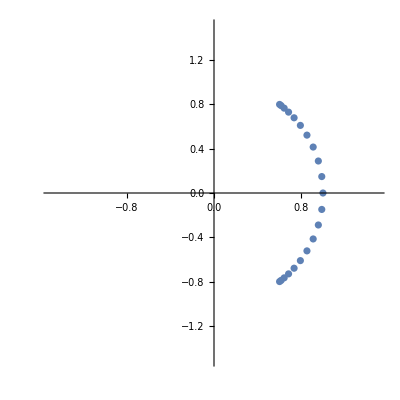

```mathematica
(*Crank–Nicolson Eigenvalues*)
evalsCN = Eigenvalues[N[MCN]];
realEvalsCN = Re[evalsCN];
imagEvalsCN = Im[evalsCN];
Abs[evalsCN]
ListPlot[Transpose[{realEvalsCN,imagEvalsCN}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

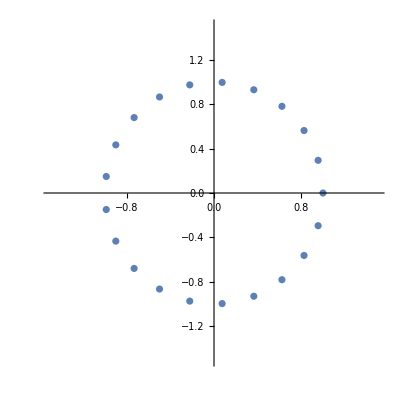

```mathematica
(*Euler*)
evalsEuler = Eigenvalues[N[euler]];
realEvalsEuler = Re[evalsEuler];
imagEvalsEuler = Im[evalsEuler];
ListPlot[{Transpose[{realEvalsEuler,imagEvalsEuler}]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999997,0.999997,0.999997,0.999997}

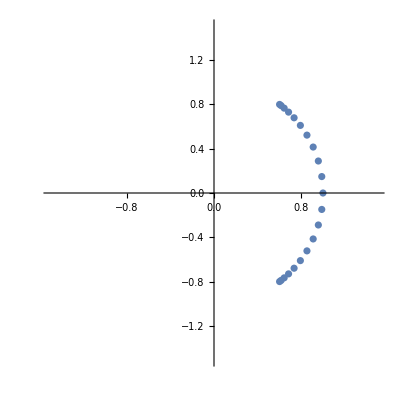

```mathematica
(*Partial Inversion*)
evalsP = Eigenvalues[N[MP//.{r-> (deltat / deltax)}]];
realEvalsP = Re[evalsP];
imagEvalsP = Im[evalsP];
Abs[evalsP]
ListPlot[{Transpose[{realEvalsP,imagEvalsP}]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

```mathematica
(************************************************************************************************************************)
(*Evolutions*)
UP = Table[0, {n, 0, Nt }, {m, 0, Nx }];
UP[[1,All]] = f[X2]//N;
UP = Chop[N[UP], 10^(-307)];
UP = N[UP];
UP = Developer`ToPackedArray[UP, Real]; 
Developer`PackedArrayQ[UP] 

Do[UP[[n+1,All]] = (MP//.{r-> (deltat / deltax)}).UP[[n,All]], {n,1,Nt}];
```

True

```mathematica
Animate[ListPlot[Table[UP[[n+1, m+1]], {m,0,Nx }], PlotRange->{All,{0,2}}], {n,0,Nt,1}]
```